```mathematica
Manipulate[
Module[{Psat,V,R,P},
Psat=10^(5.95-1500/(T+280));
V=2;(*L*)
R=0.08314;(*L bar/mol/K*)
P=n*R*(T+273)/V;

add=0.6*(0.1+(n-0.1)/(2-0.1))*(1-bn);

Graphics[{
{Thickness[0.03],Line[{{0,3},{0,3.1}}]},{FaceForm[White],EdgeForm[Thick],Rectangle[{-0.5,3.1},{0.5,3.4},RoundingRadius->0.1]},
{LightBlue,FilledCurve[{Line[{{-1,2.5},{-1,0},{1,0},{1,2.5}}],Line[Table[{x,0.5*√(1-x^2)+2.5},{x,-1,1,0.01}]]}]},
{Blue,Rectangle[{1,1.75},{1+add,2}]},
{GrayLevel[0.4],Rectangle[{1+add,1.75},{1.05+add,2}],Thickness[0.01],Line[{{1.05+add,1.875},{2.3+add,1.875}}],Black,Line[{{2.3+add,1.75},{2.3+add,2}}]},
{Thick,Line[{{-1,2.5},{-1,0},{1,0},{1,2.5}}],Line[Table[{x,0.5*√(1-x^2)+2.5},{x,-1,1,0.01}]],Line[{{1,1.75},{2.25,1.75},{2.25,2},{1,2}}]}
},ImageSize->{500,400},PlotRange->{{-1.25,4},{0,3.5}}]

],
Control[{{bn,0,"add moles of liquid"},0,1,Trigger,AnimationRate->2,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Control[{{T,30,"temperature (°C)"},25,45,1,Appearance->"Labeled"}],
Control[{{n,1,"moles of liquid"},0.1,2,0.1,Appearance->"Labeled"}]
]
```

```mathematica
2.
```

```mathematica
0.5*(1.75+2)
```

1.875

```mathematica
(*Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,0},{0,0,h}}]}
},ImageSize->{300,390},(*PlotRange->{{-1,1},{-1,1},{-0.5,6}},*)Boxed->False,(*ViewPoint->Front,*)Lighting->{{"Ambient",LightGray}}]*)
```

```mathematica
(*Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,L+V+0.25},{0,0,5.5}}]},
{GrayLevel[0.3],Cylinder[{{0,0,L+V},{0,0,L+V+0.25}}],Cylinder[{{0,0,L+V+0.25},{0,0,6}},0.17]},
{Opacity[0.75],
{Blue,Cylinder[{{0,0,0},{0,0,fL2*L}}]},
{RGBColor[0.98,0.33,0.],Cylinder[{{0,0,fL2*L},{0,0,L*(fL2+fL1)}}]},
{RGBColor[0.,0.6,0.06],Cylinder[{{0,0,L*(fL2+fL1)},{0,0,L+V}}]}},
Text[Style["log volume",17],{0,-1,-0.25}]
},ImageSize->{185,333},PlotRange->{{-1,1},{-1,1},{-0.5,6}},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}}]
*)
```

```mathematica
(*Psat=10^(Ai-Bi/(T+Ci));*)
(*Psat=10^(5.204-1734/(T+234));(*bar*)*)
```

```mathematica
(*Row[{
Column[{
Control[{{Ai,5.95,"A"},4,6,0.01,Appearance->"Labeled"}],
Control[{{Bi,1500,"B"},1500,1800,1,Appearance->"Labeled"}],
Control[{{Ci,280,"C"},200,300,1,Appearance->"Labeled"}]}],
Spacer[20],
Column[{
Control[{{T,30,"temperature (°C)"},25,45,1,Appearance->"Labeled"}],
Control[{{n,1,"moles of liquid"},0.1,2,0.1,Appearance->"Labeled"}]}]
}]*)
```

```mathematica
(*ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,π},{v,0,π},Mesh->None,Boxed->False,Axes->None]*)
(*some hemisphere*)
r=1;
d={0,0,0.5};
sphere=ParametricPlot3D[r {Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]}(*+d*),{u,-π/2,π/2},{v,-π/2,π/2},Mesh->None,Boxed->False,Axes->None][[1]];

(*Graphics3D[{sphere,Cuboid[{-5,-5,0},{5,5,0.5}]},ViewPoint->Front]*)
Graphics3D[{sphere},ViewPoint->Front]


(*SphereOpacity=0.5;
CuboidOpacity=0.5;
SphereColor=Blue;
CuboidColor=Orange;
Graphics3D[{SphereColor,Opacity[SphereOpacity],sphere,CuboidColor,Opacity[CuboidOpacity],Cuboid[{-5,-5,0},{5,5,0.5}]},Boxed->False]*)
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[u] Sin[v],Sin[u] Sin[v],Cos[v]},{u,0,π},{v,0,π},Mesh->None,Boxed->False,Axes->None]
```

-Graphics3D-

```mathematica
p1=ParametricPlot3D[{Cos[u]*Sin[v],Sin[u]*Sin[v],Cos[v]},{u,-π/2,π/2},{v,-π/2,π/2},Mesh->None,Boxed->False,Axes->None][[1]];
Graphics3D[{
Cylinder[{{0,0,0},{0,0,1}}]
},ViewPoint->Front]
```

-Graphics3D-

```mathematica
Module[{half},
half=ParametricPlot3D[{Cos[u]*Sin[v],Sin[u]*Sin[v],0.6*Cos[v]+2.5},{u,-π/2,π/2},{v,-π/2,π/2},PlotStyle->White,Mesh->None,Boxed->False,Axes->None][[1]];
Graphics3D[{
{EdgeForm[None],Opacity[0.9],Cylinder[{{0,0,0},{0,0,2.5}}]},half,
{Blue,Cylinder[{{0,0,0},{0,0,1}}]}
},ViewPoint->Front,Boxed->False]
]
```

-Graphics3D-

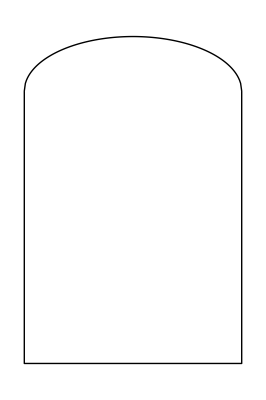

```mathematica
Graphics[{
Line[{{-1,2.5},{-1,0},{1,0},{1,2.5}}],
Line[Table[{x,0.5*√(1-x^2)+2.5},{x,-1,1,0.01}]]
}]
```

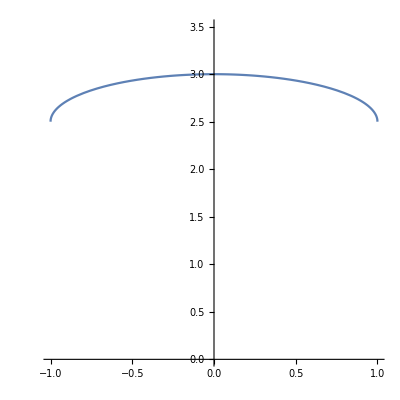

```mathematica
Plot[0.5*√(1-x^2)+2.5,{x,-1,1},AspectRatio->1,PlotRange->{{-1,1},{0,3.5}}]
```